# Практикум №1. Выявление свойств Гамма-функции

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Шклярик В.С.
  7 сентября 2021

## 2. Знакомство с Гамма-функцией

### Задание 2.1

Отыщите информацию о Гамма-функции в системе справки Mathematica

```mathematica
?Gamma[x]
```

Information[Gamma[x] ,LongForm→False]

### Задание 2.2

Постройте график Гамма-функции.

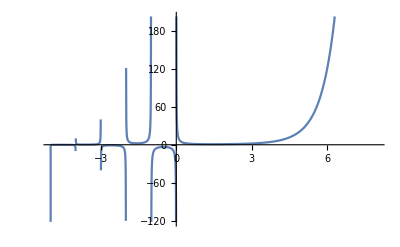

```mathematica
Plot[Gamma[x],{x,-5,8}]
```

## 3. Сравнение Гамма-функции с известными функциями

### Задание 3.1

Полюбопытствуйте, какие значения принимает Гамма-функция на множестве 
натуральных чисел.

```mathematica
Gamma/@Range[7]
```

{1,1,2,6,24,120,720}

Для натуральных значений аргумента гамма функция совпадает со значением факториала

### Задание 3.2

Сравните значения функций Гамма и Факториал.

```mathematica
Factorial/@Range[7]
```

{1,2,6,24,120,720,5040}

Γ(n + 1) = n!

```mathematica
Gamma[#+23]- Factorial[#]&/@Range[7]
```

{25852016738884976639999,620448401733239439359998,15511210043330985983999994,403291461126605635583999976,10888869450418352160767999880,304888344611713860501503999280,8841761993739701954543615994960}

Оператор Map вычисляет анонимную функцию, последовательно подставляя на место формального аргумента # каждый из элементов заданного списка.

### Задание 3.3

Постройте график дискретной функции Факториал двумя способами. В 
каждом случае используйте встроенную функцию ListPlot.

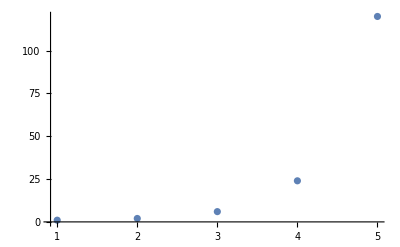

```mathematica
ListPlot[{#,#!}&/@Range[5]]
```

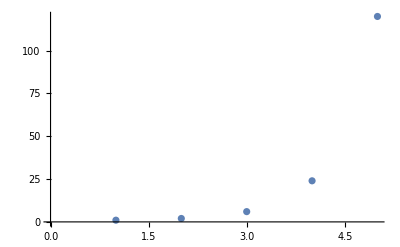

```mathematica
ListPlot[Table[x!,{x,1,5}]]
```

Функция Table реализует конструкцию повторения, вычисляет выражение x! при каждом значении локальной переменной x.

### Задание 3.4

Постройте одной и той же системе координат графики Гамма-функции и 
известных Вам элементарных функций: квадратичной, кубической, 
экспоненты e^x.

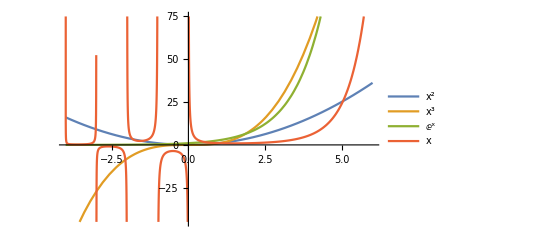

```mathematica
Plot[{x^2,x^3,ⅇ^x,Gamma[x]},{x,-4,6},PlotLegends->"Expressions"]
```

На мой взгляд, отрезок (-4;6) достаточно удобен, чтобы оценить и сравнить поведения исследуемых функций, т.к примерно на таком отрезке видно поведение каждой функции в отдельности.

### Задание 3.5

Сравните поведение Гамма-функции и известных Вам элементарных 
функций: квадратичной, кубической, экспоненты e^x.

```mathematica
Log/@{Gamma[x],x^10,ⅇ^x}
```

{Log[Gamma[x]],Log[x^10],Log[ⅇ^x]}

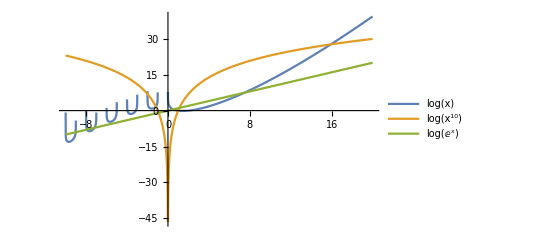

```mathematica
Plot[{Log[Gamma[x]],Log[x^10],Log[ⅇ^x]},{x,-10,20},PlotLegends->"Expressions"]
```

Гамма-функция возрастает быстрее, чем степенная или экспонента. При х>0 гамма-функция непрерывна, при x<0 прерывается.

## 4. Свойства известных функций и наша креативность

### Задание 4.1

Найдите рекуррентную формулу для вычисления значений Гамма-функции.

```mathematica
Plot[{ⅇ^(x+1)/ⅇ^x},{x,-100,100}]
```

-Graphics-

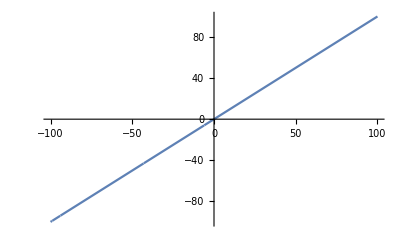

```mathematica
Plot[{Gamma[x+1]/Gamma[x]},{x,-100,100}]
```

```mathematica
Plot[{x,Gamma[x+1]/Gamma[x]},{x,-100,100},PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Options[Plot]
```

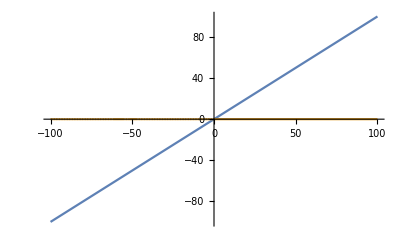

```mathematica
Plot[{x,x-Gamma[x+1]/Gamma[x]},{x,-100,100}]
```

Г(х+1)=х*Г(х)

### Задание 4.2

Получите свойство Гамма-функции, которое описывает ее связь с 
гармоническими колебаниями.

```mathematica
Plot[{ⅇ^(1-x),ⅇ^x,ⅇ},{x,-0.1,1.1},PlotLabels->"Expressions"]
```

-Graphics-

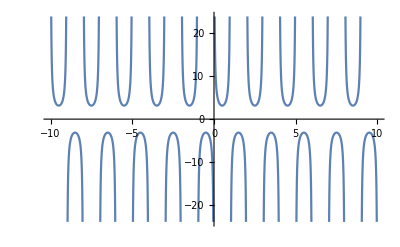

```mathematica
Plot[{Gamma[1-x]*Gamma[x]},{x,-10,10}]
```

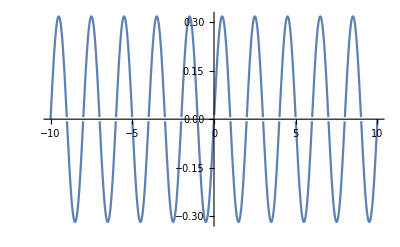

```mathematica
Plot[{1/(Gamma[1-x]*Gamma[x])},{x,-10,10}]
```

1/π

π

0

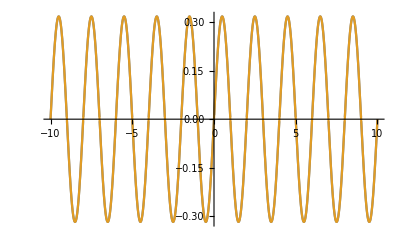

```mathematica
A=1/π
w=π
q=0
Plot[{1/(Gamma[1-x]*Gamma[x]),A*Sin[w*x+q]},{x,-10,10}]
```

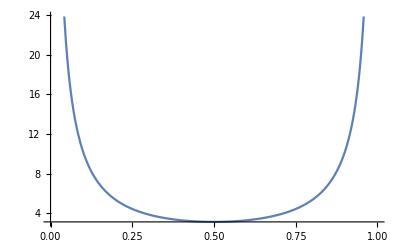

```mathematica
Plot[{Gamma[1-x]*Gamma[x]},{x,0,1}]
```

Зеркальное отображение - это полностью симметричное отображения графика относительно своей оси симметрии (в данном случае относительно прямой, проходящей через через точку х=0,5 перпендикулярно Ох).

### Задание 4.3

Сформулируйте те свойства Гамма-функции, которые Вы получили при 
приведении исследований.

Для натуральных значений аргумента гамма функция совпадает со значением факториала.
Гамма-функция возрастает быстрее, чем степенная или экспонента. При х>0 гамма-функция непрерывна, при x<0 прерывается.
Рекуррентная формула для вычисления значений Гамма-функции : Г(х+1)=х*Г(х)

## 5. Оформление результатов работы

## 6. Закрепление навыков и умений

Gamma, Plot, ListPlot, Range, Factorial, Table.